# Derivation of p(x|I_1) for J=3

```mathematica
J=n=3;
```

```mathematica
Solve[r==Log[x/c]&&s==Log[y/x]&&t==Log[z/y]&&0<c<x≤y≤z,{x,y,z},PositiveReals]//FullSimplify
a={c ⅇ^r,c ⅇ^(r+s) ,c ⅇ^(r+s+t)};
b={r,s,t};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0&&s>0&&t>0],y→ConditionalExpression[c ⅇ^(r+s),c>0&&r>0&&s>0&&t>0],z→ConditionalExpression[c ⅇ^(r+s+t),c>0&&r>0&&s>0&&t>0]}}

c^3 ⅇ^(3 r+2 s+t)

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r,s,t}]
```

ⅇ^(2 s+t)

```mathematica
Z[λ_]:=Integrate[m[{r,s,t}] Exp[-{r,s,t}.λ],{r,0,∞},{s,0,∞},{t,0,∞},Assumptions->λ∈Vectors[n,Reals]&&ρ>0]//FullSimplify
Z[{ρ,σ,τ}]
```

1/(ρ (-2+σ) (-1+τ))

```mathematica
(* Show that ρ is indeed positive, as we assumed in the integral *)
Assuming[ρ>0,D[Log[Z[{ρ,σ,τ}]],{{ρ,σ,τ},1}]==-{mr,ms,mt}]
MEsolution=Solve[%,{mr,ms,mt}][[1]]
```

{-1/ρ,-1/(-2+σ),-1/(-1+τ)}=={-mr,-ms,-mt}

{mr→1/ρ,ms→1/(-2+σ),mt→1/(-1+τ)}

The canonical ME solutions show the constraints on the Lagrange multipliers: ρ>0,σ>2,τ>1.

```mathematica
p[u_,λ_]:=(1/Z[λ]) m[u] Exp[-u.λ] (*Boole[AllTrue[u,0<#&]]*)
p[{r,s,t},{ρ,σ,τ}]
```

ⅇ^(2 s+t-r ρ-s σ-t τ) ρ (-2+σ) (-1+τ)

```mathematica
Integrate[p[{r,s,t},{ρ,σ,τ}],{r,0,∞},{s,0,∞},{t,0,∞},Assumptions->ρ>0]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,y_,z_,c_,ρ_,σ_,τ_]:=p[{Log[x/c],Log[y/x],Log[z/y]},{ρ,σ,τ}]/(x y z) Boole[0<c≤x≤y≤z]
q[x,y,z,c,ρ,σ,τ]//FullSimplify
```

Piecewise[{{c^ρ x^(-3-ρ+σ) y^(-σ+τ) z^-τ ρ (-2+σ) (-1+τ), c>0&&c≤x&&x≤y&&y≤z}, {0, True}}]

```mathematica
Integrate[q[x,y,z,c,ρ,σ,τ],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->c>0&&ρ>0]
```

1

Use the constraints on the Lagrange multipliers derived above to drastically improve MMA's performance on these integrals.

```mathematica
px[x_,c_,ρ_,σ_,τ_]=Integrate[q[x,y,z,c,ρ,σ,τ],{y,-∞,∞},{z,-∞,∞},Assumptions->0<c&&ρ>0&&σ>2&&τ>1]//FullSimplify
py[y_,c_,ρ_,σ_,τ_]=Integrate[q[x,y,z,c,ρ,σ,τ],{x,-∞,∞},{z,-∞,∞},Assumptions->0<c&&ρ>0&&σ>2&&τ>11]//FullSimplify
pz[z_,c_,ρ_,σ_,τ_]=Integrate[q[x,y,z,c,ρ,σ,τ],{x,-∞,∞},{y,-∞,∞},Assumptions->0<c&&ρ>0&&σ>2&&τ>1]//FullSimplify
```

Piecewise[{{c^ρ x^(-1-ρ) ρ, c>0&&c≤x}, {0, True}}]

Piecewise[{{(y^(-1-ρ-σ) (c^σ y^(2+ρ)-c^(2+ρ) y^σ) ρ (-2+σ))/(c^2 (2+ρ-σ)), c>0&&c<y}, {0, True}}]

Piecewise[{{(z^(-1-ρ-σ-τ) ρ (-2+σ) (-1+τ) (c^(1+τ) z^(1+ρ+σ) (2+ρ-σ)+c^(2+ρ) z^(σ+τ) (-1+σ-τ)+c^σ z^(2+ρ+τ) (-1-ρ+τ)))/(c^2 (2+ρ-σ) (1+ρ-τ) (-1+σ-τ)), c>0&&c<z}, {0, True}}]

For the moments to exist, the constraints on the Lagrange multipliers are made tighter by unit: ρ>0 turns into ρ>1, σ>2→σ>3, and so on.

```mathematica
Ex=Integrate[x px[x,c,ρ,σ,τ],{x,-∞,∞},Assumptions->0<c&&ρ>1&&σ>3&&τ>2]//FullSimplify
Ey=Integrate[y py[y,c,ρ,σ,τ],{y,-∞,∞},Assumptions->0<c&&ρ>1&&σ>3&&τ>2]//FullSimplify
Ez=Integrate[z pz[z,c,ρ,σ,τ],{z,-∞,∞},Assumptions->0<c&&ρ>1&&σ>3&&τ>2]//FullSimplify
```

(c ρ)/(-1+ρ)

(c ρ (-2+σ))/((-1+ρ) (-3+σ))

(c ρ (-2+σ) (-1+τ))/((-1+ρ) (-3+σ) (-2+τ))

## Solve for Lagrange multipliers given formant frequency first moments

It is seen that the solutions automatically enforce the constraints on the Lagrange multipliers that allowed the moments to exist in the first place. This is logical: since we assert the first moments, our ME distribution better allows them to exist. Since these enforced constraints are stricter than those implied by the ME solutions in terms of first moments of u and those necessary for Z(λ) to exist, everything is well-defined.

```mathematica
mcond=0<c<mF1<mF2<mF3;
```

```mathematica
sol=Refine[Solve[mF1==Ex&&mF2==Ey&&mF3==Ez&&mcond&&ρ>1&&σ>3&&τ>2,{ρ,σ,τ},Reals],mcond][[1]]//FullSimplify
```

{ρ→mF1/(-c+mF1),σ→3+mF1/(-mF1+mF2),τ→2+mF2/(-mF2+mF3)}

These expressions lead to the general expression for the joint p(u|X) where the hyperparameter vector X=(c,mF1,mF2,...) is zero-indexed (X_0=c,X_1=mF1,...):
	u_j ~ Exp[β_j]
Here β_j is the scale parameter of the exponential (not the rate), and is given by:
	β_j=(X_j-X_(j-1))/X_j
These expressions derive from combining the Exp[λ.u] together with the invariant measure m[u] and then noting that the joint pdf can be expressed as decoupled Exp[β_j] expressions, parametrized by scale instead of rate parameter.

## Plots

Marginals p(x_i|c,μ_(1:i)) are identical for any n≥i given the same information c,μ_(1:i). So indeed knowledge of higher formants does not influence the marginals of lower formant frequencies.

```mathematica
marginals={px[x,c,ρ,σ,τ],py[y,c,ρ,σ,τ],pz[z,c,ρ,σ,τ]}/.{y->x,z->x}/.sol/.{c->200,mF1->500,mF2->1000,mF3->1500}//N//FullSimplify
```

{Piecewise[{{11399.8/x^(8/3), 200.≤x}, {0., True}}],Piecewise[{{0., x≤200.}, {(-400000.+68399. x^(1/3))/x^3, True}}],Piecewise[{{0., x≤200.}, {(6.×10^7-1.2×10^6 x+153898. x^(4/3))/x^4, True}}]}

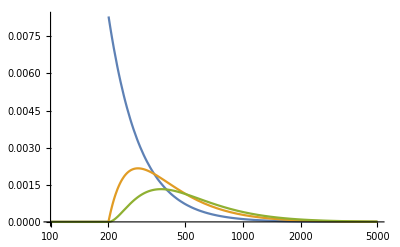

```mathematica
LogLinearPlot[marginals,{x,100,5000},PlotRange->Full]
```